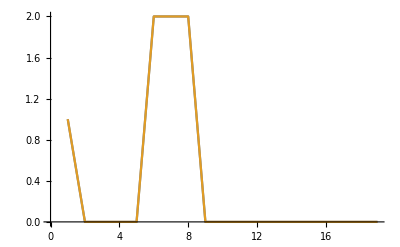

```mathematica
data1=Table[Sin[i/10],{i,0,100}]//N;
data2=Table[Sin[i/10],{i,0-10,100-10}]//N;
data1={1,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0};
data2={1,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,2,0,0};


data2={1,0,0,0,0,2,2,2,0,0,0,0,0,0,0,0,0,0,0};
ListLinePlot[{data1,data2}]
```

```mathematica
G[τ_]:=
Sum[
If[t+τ≤ Length[data1],data1[[t]]*data2[[t+τ]],0]
,{t,1,Length[data1]}]
```

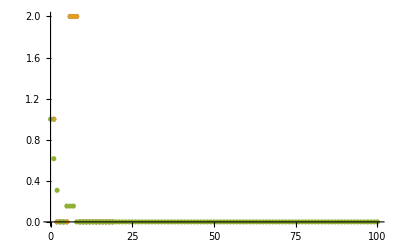

```mathematica
ListPlot[
{data1,data2,
Table[{i,G[i]/G[0]//N},{i,0,100}]
},PlotRange->All
]
```

```mathematica
taus=Table[{i,G[i]//N},{i,0,100}];
MaximalBy[taus,#[[2]]&]
```

(0 | 13.)

```mathematica
taus;
```

```mathematica
(*test1={{0.0,1.0},{1.0,0.53772849849},{2.0,0.408257275643},{3.0,0.620192789133},{6.0,0.784608579025},{7.0,0.90760540022},{8.0,0.525385138894},{9.0,0.381559155178},{10.0,0.586787112188},{14.0,0.844272388702},{15.0,0.492078520452},{16.0,0.354276972537},{17.0,0.549162038983},{20.0,0.680915805957},{21.0,0.786328487882},{22.0,0.460819755062},{23.0,0.331779043543},{24.0,0.504643915954},{27.0,0.632597000075},{28.0,0.73981147913}};
test2={{0.0,1.0},{1.0,0.535942347813},{2.0,0.409970040218},{3.0,0.6231001926},{6.0,0.786136371026},{7.0,0.916616858166},{8.0,0.52614705378},{9.0,0.387217759241},{10.0,0.594630366157},{14.0,0.862259266164},{15.0,0.498797454748},{16.0,0.363690378459},{17.0,0.562513682062},{20.0,0.696961612826},{21.0,0.811706475168},{22.0,0.471405650612},{23.0,0.343726370802},{24.0,0.524082587903},{27.0,0.656194487367},{28.0,0.769048016751}};
test3={{0.0,1.0},{1.0,0.53705529428},{2.0,0.409107591081},{3.0,0.620770959026},{6.0,0.781406877825},{7.0,0.907154691692},{8.0,0.524497125587},{9.0,0.381865059209},{10.0,0.58647403272},{14.0,0.841510864701},{15.0,0.489613335245},{16.0,0.353268984679},{17.0,0.546119844643},{20.0,0.673701549278},{21.0,0.780684626114},{22.0,0.457131767695},{23.0,0.329488029873},{24.0,0.498821293738},{27.0,0.623473025904},{28.0,0.732049936726}};
test4={{0.0,1.0},{1.0,0.534792067408},{2.0,0.410221150834},{3.0,0.622984530186},{6.0,0.784667709465},{7.0,0.916509390062},{8.0,0.525807089325},{9.0,0.387545842246},{10.0,0.596580641399},{14.0,0.862198839194},{15.0,0.499783421951},{16.0,0.36479433684},{17.0,0.562899249587},{20.0,0.695747948618},{21.0,0.811185837001},{22.0,0.472056816438},{23.0,0.344185647793},{24.0,0.522816051243},{27.0,0.654101000688},{28.0,0.769094662508}};*)
```

```mathematica
test1={{0.0,1.0},{1.0,0.529071703781},{2.0,0.40768918879},{3.0,0.632372279639},{6.0,0.77452414581},{7.0,0.909130518717},{8.0,0.522110319532},{9.0,0.384321093761},{10.0,0.600807092217},{14.0,0.853817956015},{15.0,0.49364031928},{16.0,0.358314511852},{17.0,0.565243077767},{20.0,0.681018272266},{21.0,0.800979543854},{22.0,0.465976183654},{23.0,0.338265732671},{24.0,0.530300890432},{27.0,0.647579885223},{28.0,0.768122968546}};
(7.0,0.9091305187173221)
test2={{0.0,1.0},{1.0,0.537418532727},{2.0,0.408848102327},{3.0,0.620221412678},{6.0,0.784686938125},{7.0,0.908993909941},{8.0,0.526270491675},{9.0,0.383200470486},{10.0,0.588312848627},{14.0,0.848031603419},{15.0,0.494722104049},{16.0,0.357133559797},{17.0,0.55273948913},{20.0,0.685039088362},{21.0,0.79201632918},{22.0,0.463861851647},{23.0,0.334646817944},{24.0,0.509854686292},{27.0,0.638711825406},{28.0,0.746751282244}};
(7.0,0.9089939099408509)
test3={{0.0,1.0},{1.0,0.534661014322},{2.0,0.40552240845},{3.0,0.61697128859},{6.0,0.773850087462},{7.0,0.894453361084},{8.0,0.519211961034},{9.0,0.374978749448},{10.0,0.575786279148},{14.0,0.822944281974},{15.0,0.481617236182},{16.0,0.345095870371},{17.0,0.535094565924},{20.0,0.662390728893},{21.0,0.764902112368},{22.0,0.450065583685},{23.0,0.32304644876},{24.0,0.492699996426},{27.0,0.613915111774},{28.0,0.718801373971}};
```

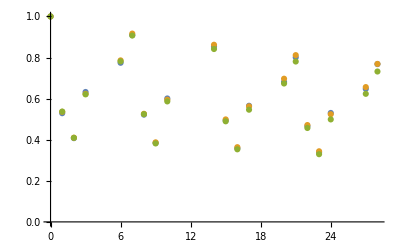

```mathematica
ListPlot[{test1,test2,test3}]
```